## Search for target sequence from all initial conditions

```mathematica
size=13;
target=RandomInteger[1,size];
max=1000;
```

```mathematica
results=Table[{init,
NestWhileList[
CellularAutomaton[110, #]&,
init, 
Last@# != target&,
max
]//Last@#==target&
},
{init, Tuples[{1,0},size]}
]
```

{{{1,1,1,1,1,1,1,1,1,1,1,1,1},False},{{1,1,1,1,1,1,1,1,1,1,1,1,0},False},{{1,1,1,1,1,1,1,1,1,1,1,0,1},False},{{1,1,1,1,1,1,1,1,1,1,1,0,0},False},{{1,1,1,1,1,1,1,1,1,1,0,1,1},False},8183,{{0,0,0,0,0,0,0,0,0,0,0,1,1},False},{{0,0,0,0,0,0,0,0,0,0,0,1,0},False},{{0,0,0,0,0,0,0,0,0,0,0,0,1},False},{{0,0,0,0,0,0,0,0,0,0,0,0,0},False}}
 |  |  |  |

```mathematica
Select[%results, TrueQ[Last@#]&]
```

{}

## How many states does rule 110 reach?

```mathematica
DeleteDuplicates[CellularAutomaton[110, RandomInteger[1,10],1000]]//Length
```

30

```mathematica
statesReached[rule_,init_, steps_]:=
Length[DeleteDuplicates[
CellularAutomaton[110, init, steps]
]]
```

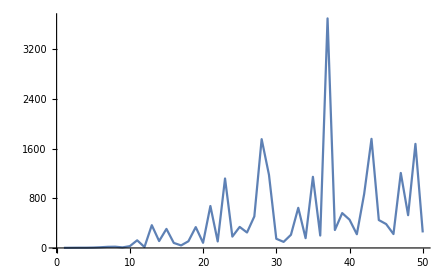

```mathematica
Table[{s,statesReached[110,CenterArray[1,s], s*100]}, {s, 1,50}]//ListLinePlot[#, PlotRange->All]&
```

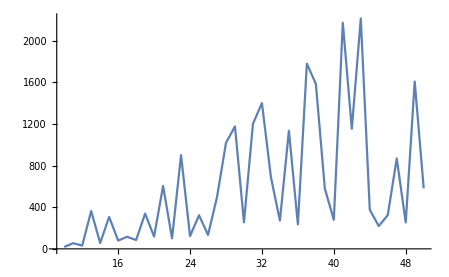

```mathematica
Table[{s,
Mean[Table[statesReached[110,i, s*100], {i, RandomInteger[1,{10,s}]}]]
}, {s, 10,50}]//
ListLinePlot[#, PlotRange->All]&
```

```mathematica
Flatten[Table[Rest@CellularAutomaton[110, init, Length@init*5], {init, Tuples[{0,1}, 10]}],1]//DeleteDuplicates//Length
```

582